# Temas de Física 1er Examen

```mathematica
ClearAll["Global`*"]
```

```mathematica
Tabla[F_,a_,b_,p__:0.5]:=Table[F==r,{r,a,b,p}]
```

```mathematica
CN1x1[F_,r_]:=ContourPlot[Evaluate[F[x,y]==r],{x,-9,9},{y,-9,9},ImageSize->{1000,1000},ContourStyle->Directive[White,Thick]];
```

```mathematica
LinCam[f_,g_,n_:4]:={StreamDensityPlot[{f[x,y],g[x,y]},{x,-1*n,n},{y,-1*n,n},ColorFunction->"SunsetColors"(*GrayYellowTones*),StreamStyle->Yellow,StreamScale->Tiny,StreamPoints->Fine,PerformanceGoal->"Quality",PlotRange->3],StreamPlot[{f[x,y],g[x,y]},{x,-1,1},{y,-1,1},ColorFunction->Invisible,StreamStyle->Yellow,StreamScale->Tiny,StreamPoints->Tuples[{0.05,-0.05},2]]};(*Esta función grafica los stramlines*)
```

```mathematica
Showing[g1_,g2_,g3___,g4___,g5___]:=Show[{g1,g2,g3,g4,g5},PlotRange->{{-3,3},{-3,3}},AxesLabel->{"x",HoldForm["y"]},PlotLabel->HoldForm["Sistema no lineal"],Axes->True,Frame->True,ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->18,FontColor->RGBColor[0,0,0.4]}] (*Esta función muestra los plots*)
```

```mathematica
CurvaNivel[F_,a_,b_,paso_:0.5]:=ContourPlot[Evaluate[Tabla[F[x,y],a,b,paso]],{x,-9,9},{y,-9,9},ImageSize->{1000,1000},ContourStyle->Directive[White,Thick]];
```

```mathematica
Singularidades[f_,g_]:=Solve[{f[x,y]==0,g[x,y]==0}](*Esta función devuelve las singularidades REALES*)
```

```mathematica
Points[f_,g_]:=Graphics[{PointSize[0.015],Yellow,Point[Table[{x,y}/.Select[Singularidades[f,g],FreeQ[#,Complex]&][[i]],{i,Dimensions[Select[Singularidades[f,g],FreeQ[#,Complex]&]][[1]]}]]}](*Esta función grafica los puntos de las singularidades*)
```

```mathematica
JacMatrix[f_,g_]:={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}}//MatrixForm;(*Esta función devuelve la matriz Jacobiana*)
```

```mathematica
Jac[f_,g_]:={{D[f[x,y],x],D[f[x,y],y]},{D[g[x,y],x],D[g[x,y],y]}};(*Esta función devuelve lo anterior pero no en forma de matriz*)
```

```mathematica
ode[f_,g_,x0_,y0_,ti_,tf_:10]:=NDSolve[{x'[t]==f[x[t],y[t]],y'[t]==g[x[t],y[t]],x[0]==x0,y[0]==y0},{x[t],y[t]},{t,ti,tf},MaxSteps->Infinity];(*Esta función produce una sola solución*)
p[f_,g_,x0_,y0_,ti_,tf_:10]:=ParametricPlot[Evaluate[Table[{x[t],y[t]}/.ode[f,g,x0,y0,ti,tf]],{t,ti,tf},PlotStyle->{Cyan,Thick}, PlotRange->{{-3,3},{-3,3}},PlotPoints->1000,AxesLabel->{"x","y"}]];(*Esta función grafica una solución*)
```

```mathematica
FuncionH[H_]:=Plot3D[H[x,y],{x,-3,3},{y,-3,3},BoxRatios->{1,1,1},ImageSize->{1000,1000},AspectRatio->1,BaseStyle->{FontFamily->"Times",FontSize->20},ColorFunction->"NeonColors",AxesLabel->Automatic,PlotLegends->Automatic]
```

# Pregunta 2

a) Establecer el sistema correspondiente a la función Hamiltoniana:

```mathematica
H1[x,y]:= y^2/2 + x^2/2 - x^4/4
```

analizar las singularidades , establecer mediante curvas de nivel, el retrato de fase y graficar la función Hamiltoniana.

Piecewise[{{ẋ=, (∂H[x,y])/(∂y)}, {ẏ=, -(∂H[x,y])/(∂x)}}]=f[x,y]
=g[x,y]

```mathematica
f1[x_,y_]=(∂H1[x,y])/(∂y)
```

y

```mathematica
g1[x_,y_]=-(∂H1[x,y])/(∂x)
```

-x+x^3

Ubicando las singularidades:

```mathematica
p1=Singularidades[f1,g1]
```

{{x→-1,y→0},{x→0,y→0},{x→1,y→0}}

Analizando las singularidades

En este caso hay 3 singularidades. Estableciendo la matriz Jacobiana:

```mathematica
J1=JacMatrix[f1,g1]
```

(0 | 1
-1+3 x^2 | 0)

Evaluando la matriz Jacobiana en P1:

```mathematica
p1[[1]]
```

{x→-1,y→0}

```mathematica
J1/.p1[[1]]//MatrixForm
```

(0 | 1
2 | 0)

Obteniendo los autovalores:

```mathematica
Jac[f1,g1]/.p1[[1]]//Eigenvalues
```

{-√2,√2}

Observamos que es un punto singular hiperbólico  y se puede aplicar el teorema de Hartman. En el sistema lineal resultado de la linealización en un entrono cercano a P1(-1,0), la singularidad (trasladada al origen) tiene un comportamiento cualitativo de tipo “ensilladura”.

Evaluando la matriz Jacobiana en P2:

```mathematica
p1[[2]]
```

{x→0,y→0}

```mathematica
J1/.p1[[2]]//MatrixForm
```

(0 | 1
-1 | 0)

Obteniendo los autovalores:

```mathematica
Jac[f1,g1]/.p1[[2]]//Eigenvalues
```

{ⅈ,-ⅈ}

Observamos que no es un punto singular hiperbólico  y se puede aplicar el Teorema de Lyapunov. Provemos con V(x,y)= H(x,y)= y^2/2 + x^2/2 - x^4/4

```mathematica
V1[x_,y_]:= y^2/2 + x^2/2 - x^4/4
```

```mathematica
V1[0,0]
```

0

```mathematica
Grad[V1[x,y],{x,y}]
```

{x-x^3,y}

```mathematica
fun1={f1[x,y],g1[x,y]}.Grad[V1[x,y],{x,y}]//Simplify
```

0

Evaluando la matriz Jacobiana en P3:

```mathematica
p1[[3]]
```

{x→1,y→0}

```mathematica
J1/.p1[[3]]//MatrixForm
```

(0 | 1
2 | 0)

Obteniendo los autovalores:

```mathematica
Jac[f1,g1]/.p1[[3]]//Eigenvalues
```

{-√2,√2}

Observamos que es un punto singular hiperbólico  y se puede aplicar el teorema de Hartman. En el sistema lineal resultado de la linealización en un entrono cercano a P3(1,0), la singularidad (trasladada al origen) tiene un comportamiento cualitativo de tipo "ensilladura".

Graficando:

```mathematica
P1=Points[f1,g1];(*Graficando las singularidades*)
```

```mathematica
P21=CurvaNivel[H1,1,5,1];(*Grafica las Curvas de Nivel en BLANCO*)
```

```mathematica
P23={CN1x1[H1,0.5],CN1x1[H1,0.25],CN1x1[H1,0.05],CN1x1[H1,-1]};(*Grafica algunas las Curvas de Nivel 1x1 en BLANCO*)
```

```mathematica
P3=LinCam[f1,g1,3];(*Graficando Lineas de Corriente*)
```

```mathematica
P4={p[f1,g1, -1,-1,-3.2937699501887168, 10],p[f1,g1,-0.2,-1, -2.9999120830686,2.604],p[f1,g1,-0.2,-1,-2.9999120, 2.604998],p[f1,g1,-2,-0.5,-0.1438409472846036, 0.9282083875258937],p[f1,g1,-2,-2,-0.6118228079146491,0.7853980975403203],p[f1,g1,1,-1,-0.6118228079146491,10],p[f1,g1,0.2,-1,-10,10],p[f1,g1,0.1,-0.1,-10,10],p[f1,g1,2,-0.5,-0.1438409472846036,10],p[f1,g1,2,-2,-0.1438409472846036,10],p[f1,g1,-1,1,-10,10],p[f1,g1,-0.2,1,-10,10],p[f1,g1,-0.1,0.1,-10,10],p[f1,g1,-2,2,-0.1438409472846036,10],p[f1,g1,1,1,-10,10],p[f1,g1,0.2,1,-10,10],p[f1,g1,0.1,0.1,-10,10],p[f1,g1,2,0.5,-10,10],p[f1,g1,2,2,-0.1438409472846036,10],p[f1,g1,-2,0.5,-10,10],p[f1,g1,-0.8,0.5,-10,10],p[f1,g1,0.8,-0.5,-10,10],p[f1,g1,-0.6,0,-10,10]};(*Retrato de fase del sistema considerando 20 curvas solución EN CYAN*)
```

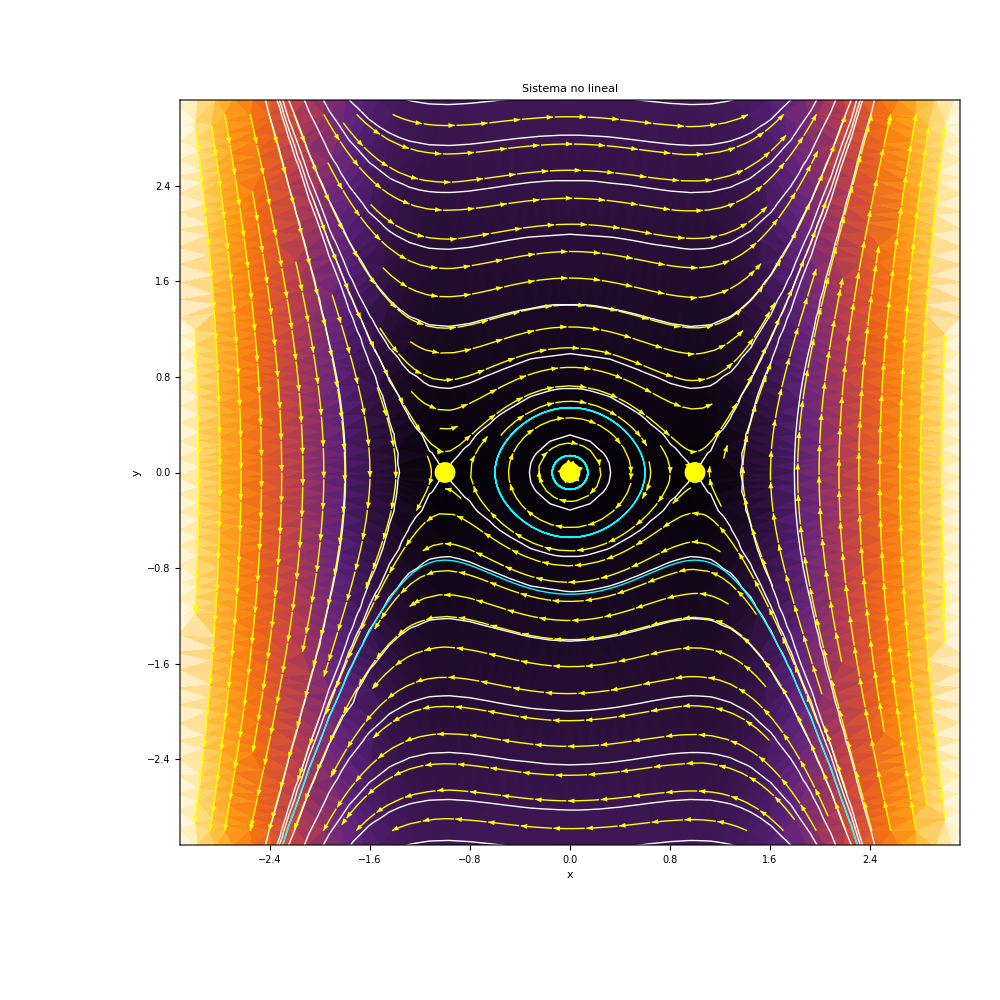

```mathematica
Showing[P3,P21,P23,P1,P4](*Muestra los gráficos*)
```

```mathematica
FuncionH[H1]
```

-Graphics3D-

b) Analizar si el siguiente sistema es un sistema Hamiltoniano. En caso afirmativo, analizar sus singularidades, establecer el retrato de fase mediante curvas de nivel y  graficar la función Hamiltoniana corresponde:

Piecewise[{{ẋ, =y}, {ẏ, =x-x^3}}] =
=(∂H[x,y])/(∂y)
-(∂H[x,y])/(∂x)=f[x,y]
=g[x,y]

Definiendo las funciones componentes del campo vectorial asociado al sistema:

```mathematica
f2[x_,y_]=y;
g2[x_,y_]=x-x^3;
```

```mathematica
H2[x,y]=Integrate[f2[x,y],y]-Integrate[g2[x,y],x]
```

-x^2/2+x^4/4+y^2/2

Ubicando las singularidades:

```mathematica
p2=Singularidades[f2,g2]
```

{{x→-1,y→0},{x→0,y→0},{x→1,y→0}}

Analizando las singularidades

En este caso hay 3 singularidades. Estableciendo la matriz Jacobiana:

```mathematica
J2=JacMatrix[f2,g2]
```

(0 | 1
1-3 x^2 | 0)

Evaluando la matriz Jacobiana en P1:

```mathematica
p2[[1]]
```

{x→-1,y→0}

```mathematica
J2/.p2[[1]]//MatrixForm
```

(0 | 1
-2 | 0)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/.p2[[1]]//Eigenvalues
```

{ⅈ √2,-ⅈ √2}

Observamos que no es un punto singular hiperbólico .

Evaluando la matriz Jacobiana en P2:

```mathematica
p2[[2]]
```

{x→0,y→0}

```mathematica
J2/.p2[[1]]//MatrixForm
```

(0 | 1
-2 | 0)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/.p2[[2]]//Eigenvalues
```

{-1,1}

Observamos que es un punto singular hiperbólico  y se puede aplicar el teorema de Hartman. En el sistema lineal resultado de la linealización en un entrono cercano a P2(0,0), la singularidad tiene un comportamiento cualitativo de tipo “ensilladura”.

Evaluando la matriz Jacobiana en P3:

```mathematica
p2[[3]]
```

{x→1,y→0}

```mathematica
J2/.p2[[3]]//MatrixForm
```

(0 | 1
-2 | 0)

Obteniendo los autovalores:

```mathematica
Jac[f2,g2]/.p2[[3]]//Eigenvalues
```

{ⅈ √2,-ⅈ √2}

Observamos que es un punto no singular hiperbólico .

Graficando:

```mathematica
M1=Points[f2,g2];(*Graficando las singularidades*)
```

```mathematica
M21=CurvaNivel[H2,1,5,1];(*Grafica las Curvas de Nivel en BLANCO*)
```

```mathematica
M23={CN1x1[H2,0.5],CN1x1[H2,0.25],CN1x1[H2,0.05],CN1x1[H2,0.0000005]};(*Grafica algunas las Curvas de Nivel 1x1 en BLANCO*)
```

```mathematica
M3=LinCam[f2,g2,3];(*Graficando Lineas de Corriente*)
```

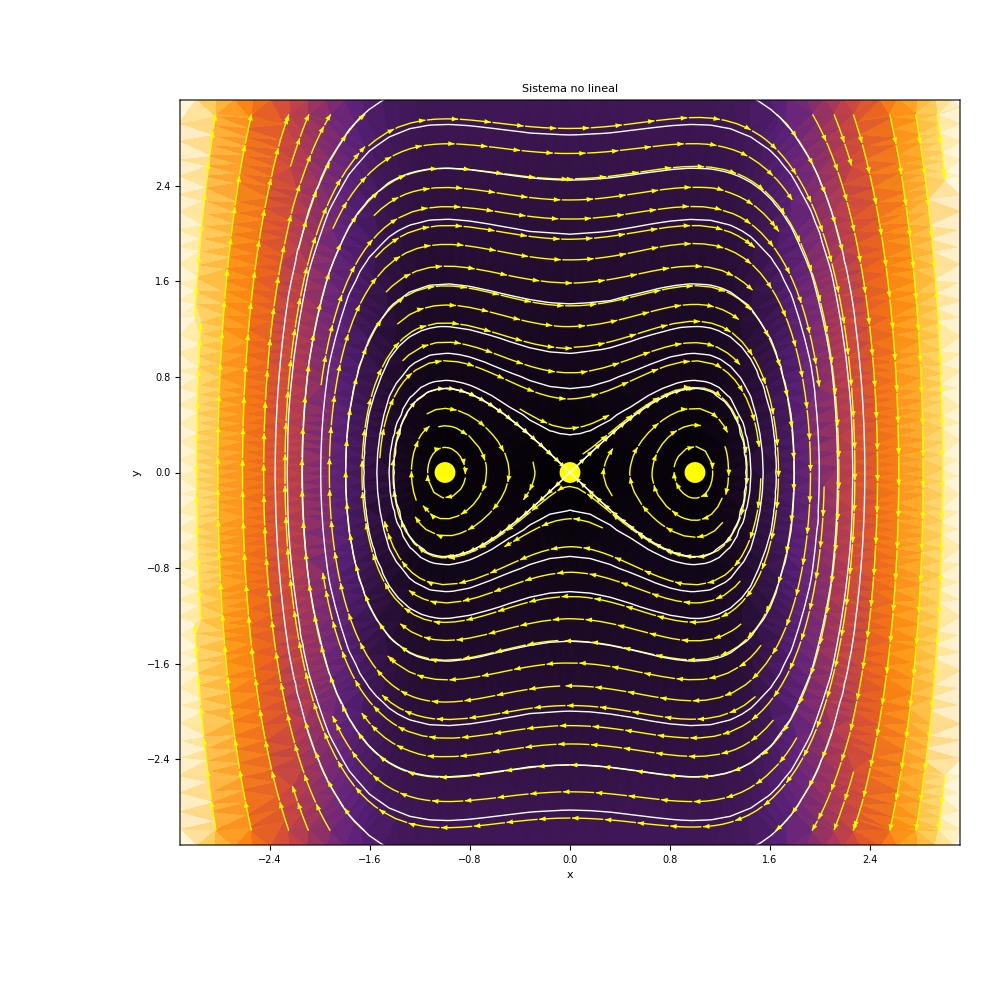

```mathematica
Showing[M3,M21,M1,M23](*Muestra los gráficos*)
```

```mathematica
FuncionH[H2]
```

-Graphics3D-